```mathematica
x = xo - xs;
y = yo - ys;
C0 = 1/ (4 * Pi *(1-ν));
r = Sqrt[x^2 + y^2];
g = -C0 * Log[r];
gx = -C0*x/r^2;
gy = -C0*y/r^2;
gxy = 2*C0*x*y/r^4;
gxx = C0*(x^2 - y^2)/r^4;
gyy = -gxx;
ux = fx/(2*μ)*((3-4*ν)*g - x*gx) + fy/(2*μ)*(-y*gx) ;
uy = fx/(2*μ)*(-x*gy) + fy/(2*μ)*((3-4*ν)*g -y*gy);
sxx = fx*(2*(1 - ν)*gx - x*gxx) + fy*(2*ν* gy - y*gxx)
syy = fx*(2*ν*gx - x*gyy) + fy * (2*(1 - ν)*gy - y*gyy)
sxy = fx*((1 - 2*ν)*gy - x*gxy) + fy*((1 - 2*ν)*gx - y*gxy)
```

fx (-(xo-xs)/(2 π ((xo-xs)^2+(yo-ys)^2))-((xo-xs) ((xo-xs)^2-(yo-ys)^2))/(4 π ((xo-xs)^2+(yo-ys)^2)^2 (1-ν)))+fy (-(((xo-xs)^2-(yo-ys)^2) (yo-ys))/(4 π ((xo-xs)^2+(yo-ys)^2)^2 (1-ν))-((yo-ys) ν)/(2 π ((xo-xs)^2+(yo-ys)^2) (1-ν)))

fy (-(yo-ys)/(2 π ((xo-xs)^2+(yo-ys)^2))+(((xo-xs)^2-(yo-ys)^2) (yo-ys))/(4 π ((xo-xs)^2+(yo-ys)^2)^2 (1-ν)))+fx (((xo-xs) ((xo-xs)^2-(yo-ys)^2))/(4 π ((xo-xs)^2+(yo-ys)^2)^2 (1-ν))-((xo-xs) ν)/(2 π ((xo-xs)^2+(yo-ys)^2) (1-ν)))

fy (-((xo-xs) (yo-ys)^2)/(2 π ((xo-xs)^2+(yo-ys)^2)^2 (1-ν))-((xo-xs) (1-2 ν))/(4 π ((xo-xs)^2+(yo-ys)^2) (1-ν)))+fx (-((xo-xs)^2 (yo-ys))/(2 π ((xo-xs)^2+(yo-ys)^2)^2 (1-ν))-((yo-ys) (1-2 ν))/(4 π ((xo-xs)^2+(yo-ys)^2) (1-ν)))

```mathematica
sxymod = ReplaceAll[sxy,{ys->0,yo->0.001}];
sxyint = Re[Integrate[sxymod,{xs,-1,1},Assumptions->{Im[xo]==0,-1<=Re[xo]<=1} ]];

sxxmod = ReplaceAll[sxx,{ys->0,yo->0.001}];
sxxint = Re[Integrate[sxxmod,{xs,-1,1},Assumptions->{Im[xo]==0,-1<=Re[xo]<=1} ]];

syymod = ReplaceAll[syy,{ys->0,yo->0.001}];
syyint = Re[Integrate[syymod,{xs,-1,1},Assumptions->{Im[xo]==0,-1<=Re[xo]<=1} ]];
```

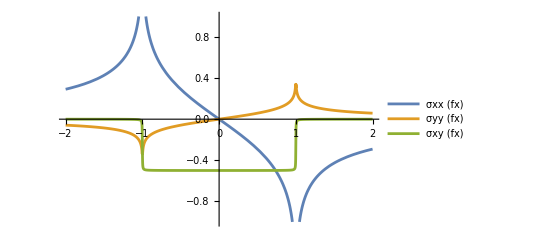

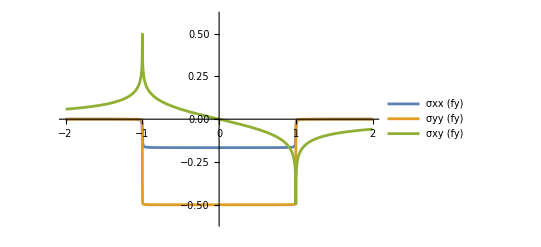

```mathematica
Plot[{ReplaceAll[sxxint,{fx -> 1,fy->0, μ->1,ν->0.25}],ReplaceAll[syyint,{fx -> 1,fy->0, μ->1,ν->0.25}],ReplaceAll[sxyint,{fx -> 1,fy->0, μ->1,ν->0.25}]},{xo,-2,2},PlotLegends->{"σxx (fx)","σyy (fx)","σxy (fx)"},PlotRange->{-1,1}]
Plot[{ReplaceAll[sxxint,{fx -> 0,fy->1, μ->1,ν->0.25}],ReplaceAll[syyint,{fx -> 0,fy->1, μ->1,ν->0.25}],ReplaceAll[sxyint,{fx -> 0,fy->1, μ->1,ν->0.25}]},{xo,-2,2},PlotLegends->{"σxx (fy)","σyy (fy)","σxy (fy)"},PlotRange->{-0.6,0.6}]
```

```mathematica
SXYindef = Integrate[sxy,xs,GeneratedParameters->C];
SXYdef = ReplaceAll[SXYindef,{xs->1}]-ReplaceAll[SXYindef,{xs->-1}]//FullSimplify

SXXindef = Integrate[sxx,xs,GeneratedParameters->C];
(*SXXdef = ReplaceAll[SXXindef,{xs->1}]-ReplaceAll[SXXindef,{xs->-1}]//FullSimplify*)
SXXdef = 1/(4 π (-1+ν))(-(2 (fy (1-xo^2+(yo-ys)^2)+2 fx xo (yo-ys)) (yo-ys))/((1+(-2+xo) xo+(yo-ys)^2) (1+xo (2+xo)+(yo-ys)^2))+2 fy ν (ArcTan[xo-1,yo-ys]-ArcTan[xo+1,yo-ys])+1/2 fx (-3+2 ν) (Log[1+(-2+xo) xo+(yo-ys)^2]-Log[1+xo (2+xo)+(yo-ys)^2]));(*manually fixed issue with ArcTan branch cuts*)
(*SXXnumeric = NIntegrate[sxxmod,{xs,-1,1},MaxRecursion->20,opts];*)

SYYindef = Integrate[syy,xs,GeneratedParameters->C];
SYYdef = ReplaceAll[SYYindef,{xs->1}]-ReplaceAll[SYYindef,{xs->-1}]//FullSimplify
```

-((2 (yo-ys) (fx (1-xo^2+(yo-ys)^2)+2 fy xo (-yo+ys)))/((1+(-2+xo) xo+(yo-ys)^2) (1+xo (2+xo)+(yo-ys)^2))-2 fx (-1+ν) ArcTan[(-1+xo)/(yo-ys)]+2 fx (-1+ν) ArcTan[(1+xo)/(yo-ys)]+1/2 fy (-1+2 ν) (-Log[1+(-2+xo) xo+(yo-ys)^2]+Log[1+xo (2+xo)+(yo-ys)^2]))/(4 π (-1+ν))

((2 (fy (1-xo^2+(yo-ys)^2)+2 fx xo (yo-ys)) (yo-ys))/((1+(-2+xo) xo+(yo-ys)^2) (1+xo (2+xo)+(yo-ys)^2))+2 fy (-1+ν) ArcTan[(-1+xo)/(yo-ys)]-2 fy (-1+ν) ArcTan[(1+xo)/(yo-ys)]-1/2 fx (-1+2 ν) (Log[1+(-2+xo) xo+(yo-ys)^2]-Log[1+xo (2+xo)+(yo-ys)^2]))/(4 π (-1+ν))

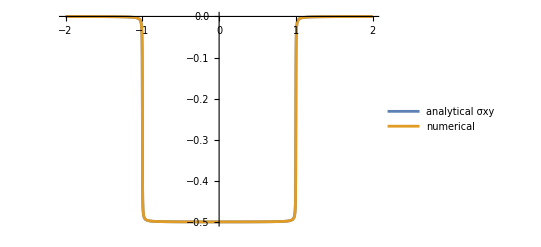

```mathematica
Plot[{ReplaceAll[sxyint,{fx -> 1,fy->0, μ->1,ν->0.25}],ReplaceAll[SXYdef,{fx -> 1,fy->0, μ->1,ν->0.25,ys->0,yo->0.001}]},{xo,-2,2},PlotLegends->{"analytical σxy","numerical"}]
```

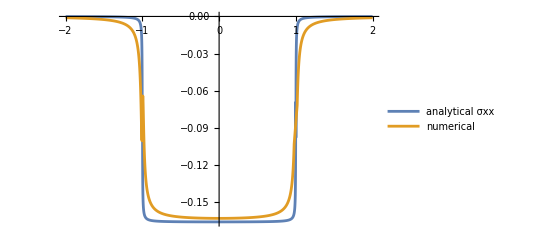

```mathematica
Plot[{ReplaceAll[sxxint,{fx -> 0,fy->1, μ->1,ν->0.25}],ReplaceAll[SXXdef,{fx -> 0,fy->1, μ->1,ν->0.25,ys->0,yo->0.01}]},{xo,-2,2},PlotLegends->{"analytical σxx","numerical"}]
```

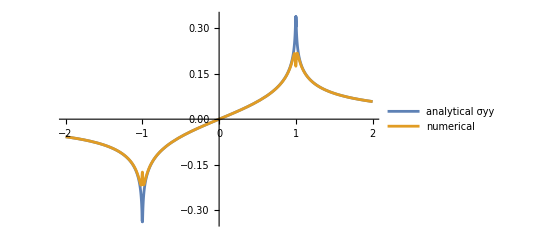

```mathematica
Plot[{ReplaceAll[syyint,{fx -> 1,fy->0, μ->1,ν->0.25}],ReplaceAll[SYYdef,{fx -> 1,fy->0, μ->1,ν->0.25,ys->0,yo->0.01}]},{xo,-2,2},PlotLegends->{"analytical σyy","numerical"}]
```

```mathematica
p1 = Plot[{ReplaceAll[SXXdef,{fx -> 1,fy->0, μ->1,ν->0.25,ys->0,yo->0.001}],ReplaceAll[SYYdef,{fx -> 1,fy->0, μ->1,ν->0.25,ys->0,yo->0.001}],ReplaceAll[SXYdef,{fx -> 1,fy->0, μ->1,ν->0.25,ys->0,yo->0.001}]},{xo,-2,2},PlotLegends->{Subscript["σ", "xx"],Subscript["σ", "yy"],Subscript["σ", "xy"]},PlotLabel->Style[Row[{Subscript["f","x"]," = 1,  ",Subscript["f","y"]," = 0"}],14],ImageSize->Medium,PlotRange->{-1,1}];
p2 = Plot[{ReplaceAll[SXXdef,{fx -> 0,fy->1, μ->1,ν->0.25,ys->0,yo->0.001}],ReplaceAll[SYYdef,{fx -> 0,fy->1, μ->1,ν->0.25,ys->0,yo->0.001}],ReplaceAll[SXYdef,{fx -> 0,fy->1, μ->1,ν->0.25,ys->0,yo->0.001}]},{xo,-2,2},PlotLegends->{Subscript["σ", "xx"],Subscript["σ", "yy"],Subscript["σ", "xy"]},PlotLabel->Style[Row[{Subscript["f","x"]," = 0,  ",Subscript["f","y"]," = 1"}],14],ImageSize->Medium, PlotRange->{-1,1}];
GraphicsRow[{p1,p2},ImageSize->Full]
```

-Graphics-

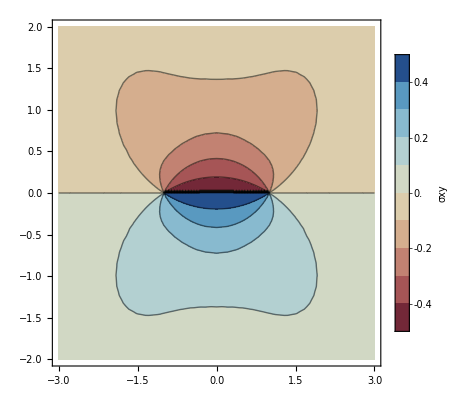
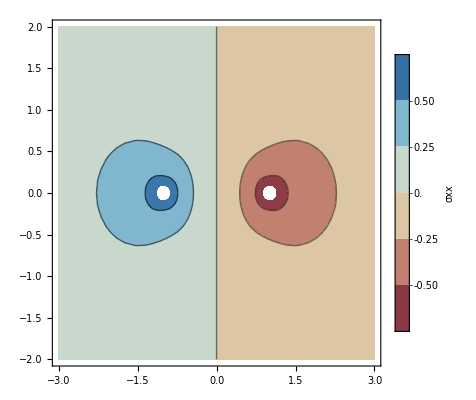
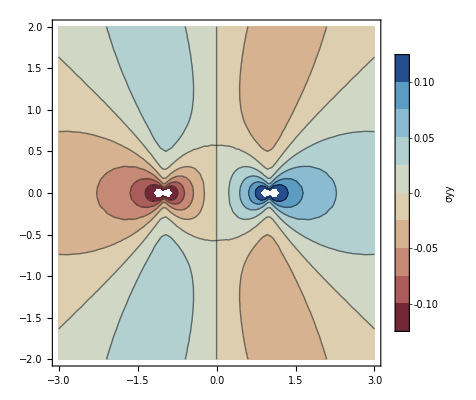

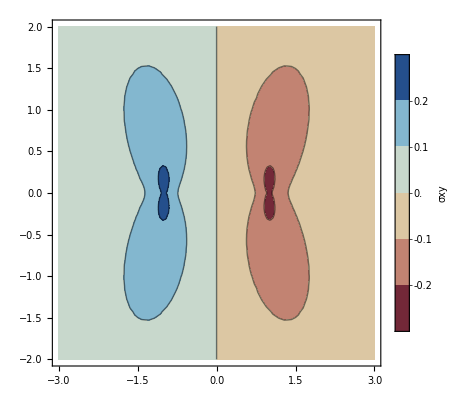
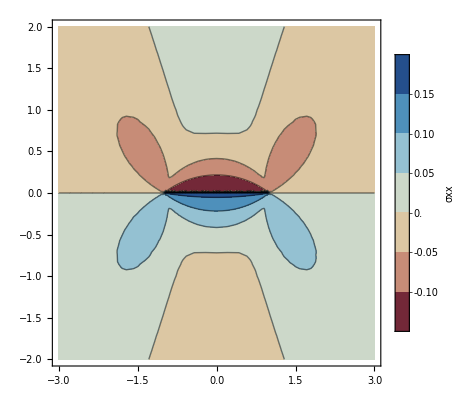
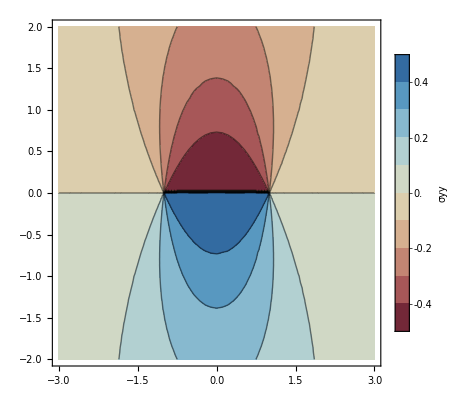

```mathematica
{ContourPlot[ReplaceAll[SXYdef,{fx->1,fy->-0,μ->1,ν->0.25,ys->0}],{xo,-3,3},{yo,-2,2},PlotLegends->BarLegend[Automatic,LegendLabel->"σxy"],ColorFunction->"RedBlueTones"],
ContourPlot[ReplaceAll[SXXdef,{fx->1,fy->-0,μ->1,ν->0.25,ys->0}],{xo,-3,3},{yo,-2,2},PlotLegends->BarLegend[Automatic,LegendLabel->"σxx"],ColorFunction->"RedBlueTones"],
ContourPlot[ReplaceAll[SYYdef,{fx->1,fy->-0,μ->1,ν->0.25,ys->0}],{xo,-3,3},{yo,-2,2},PlotLegends->BarLegend[Automatic,LegendLabel->"σyy"],ColorFunction->"RedBlueTones"]}
{ContourPlot[ReplaceAll[SXYdef,{fx->0,fy->1,μ->1,ν->0.25,ys->0}],{xo,-3,3},{yo,-2,2},PlotLegends->BarLegend[Automatic,LegendLabel->"σxy"],ColorFunction->"RedBlueTones"],
ContourPlot[ReplaceAll[SXXdef,{fx->0,fy->1,μ->1,ν->0.25,ys->0}],{xo,-3,3},{yo,-2,2},PlotLegends->BarLegend[Automatic,LegendLabel->"σxx"],ColorFunction->"RedBlueTones"],
ContourPlot[ReplaceAll[SYYdef,{fx->0,fy->1,μ->1,ν->0.25,ys->0}],{xo,-3,3},{yo,-2,2},PlotLegends->BarLegend[Automatic,LegendLabel->"σyy"],ColorFunction->"RedBlueTones"]}
```

-(0.106103 yo ((xo-xs)^2-yo^2))/(((xo-xs)^2+yo^2)^2)-(0.0530516 yo)/((xo-xs)^2+yo^2)

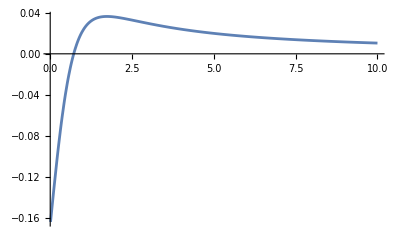

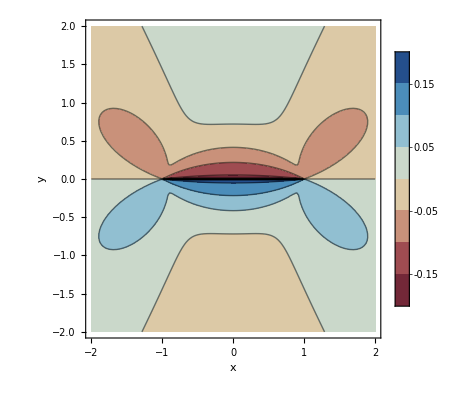

```mathematica
dummy=ReplaceAll[sxx,{ys->0,μ->1,ν->0.25,fx->0,fy->1}]
(*ReplaceAll[syy,{ys->0,μ->1,ν->0.25,fx->0,fy->1}]*)
intfun=Function[{xsf,xof,yof},dummy/.{xs->xsf,xo->xof,yo->yof}];
lineIntegral[x_?NumericQ,y_?NumericQ]:=Module[{f},f[xs_?NumericQ]:=intfun[xs,x,y];NIntegrate[f[x0],{x0,-1,1}]];
Plot[lineIntegral[0,y],{y,0.01,10},PlotRange->Full]
ContourPlot[lineIntegral[x,y],{x,-2,2},{y,-2,2},PlotPoints->40,ColorFunction->"RedBlueTones",FrameLabel->{"x","y"},PlotLegends->Automatic,PlotRange->Full]
```